```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY196/sec_int_data/778nm.dat"]
```

{{1.64105,-0.0464524},{1.57964,-0.0549315},{1.51907,-0.0353371},{1.47433,-0.0341671},{1.70936,-0.0417808},{1.78557,-0.0572584}}

0.0472479-0.0570001 x

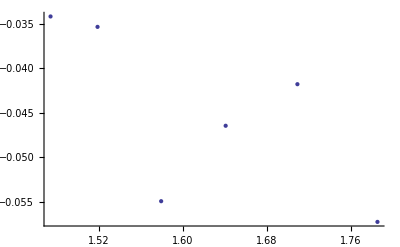

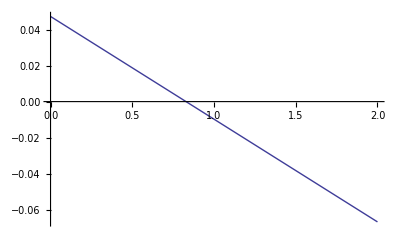

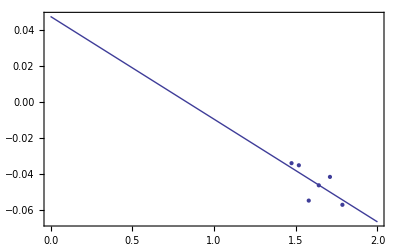

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```